```mathematica
SetDirectory[NotebookDirectory[]];Get["library/FeynCalc.m"]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File object.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_], LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

```mathematica
FCSetDiracGammaScheme["BMHV"]
```

BMHV

```mathematica
$Assumptions={d>0,e>0,m> 0,v>0,ϵ>0,Λ>1}
```

{d>0,e>0,m>0,v>0,ϵ>0,Λ>1}

```mathematica
wick[indices_,P_]:=Module[{l=Length[indices],intindices,i,ix,f,g,J1,J2,J3},intindices=Table[ix[i],{i,1,l}];f[s_]:=MTd[s[[1]],s[[2]]] Signature[s]^P;g[S_]:=Apply[Times,Map[f,Partition[S,2]]];J1=Map[g,Select[Permutations[intindices],Signature[#]==1&]];J2=Map[g,Select[Permutations[intindices],Signature[#]==-1&]];
J3=1/((l/2)!2^(l/2))(Total[J1]+(-1)^P Total[J2])//FullSimplify;J3//.Thread[intindices-> indices]]
```

```mathematica
intcont[q_,d_,indices_]:=Module[{l=Length[indices],norm},norm=1/(Pochhammer[d/2,l/2] 2^(l/2));If[EvenQ[l],norm q^l wick[indices,0],0]//FullSimplify]
```

```mathematica
FVd[q_,i_]:=Pair[LorentzIndex[i,d],Momentum[q,d]]
```

```mathematica
MTd[i_,j_]:=Pair[LorentzIndex[i,d],LorentzIndex[j,d]]
```

```mathematica
LCdC[i_,j_,k_,l_,m_,n_]:=MTd[i,l](MTd[j,m]MTd[k,n]-MTd[j,n]MTd[k,m])-MTd[i,m](MTd[j,l]MTd[k,n]-MTd[j,n]MTd[k,l])+MTd[i,n](MTd[j,l]MTd[k,m]-MTd[j,m]MTd[k,l])
```

```mathematica
SPd[p_,q_]:=Pair[Momentum[p,d],Momentum[q,d]]
```

```mathematica
dband[q_,L_]:=Module[{i,j},√(d/(2(d-1)))Contract[GSD[L[i,j]]FVd[q,i]FVd[q,j]]]
```

```mathematica
G[w_,q_,L_]:=(-I w+dband[q,L]/(2m))/(w^2+SPd[q,q]^2/(4 m^2))
```

```mathematica
D0[w_,q_]:=(v SPd[q,q])/(w^2+v SPd[q,q]^2)
```

```mathematica
D1[w_,q_,i_,j_]:=MTd[i,j]/(w^2+v SPd[q,q]^2)
```

```mathematica
C0=-I e ;
```

```mathematica
C1[q_,L_,i_]:=Module[{j},-e(√(d/(2(d-1)))Contract[GSD[L[i,j]]FVd[q,j]]/(2m))]
```

```mathematica
CubeAniso[q_,qarr_,t_,u_,k_,m_]:=-Pair[LorentzIndex[k,d],Momentum[q,d]] Pair[LorentzIndex[m,d],Momentum[q,d]] Pair[LorentzIndex[t,d],LorentzIndex[u,d]] qarr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[u,d]] Pair[LorentzIndex[m,d],Momentum[q,d]] Pair[LorentzIndex[t,d],Momentum[q,d]] qarr[q,{t,u}]+Pair[LorentzIndex[k,d],Momentum[q,d]] Pair[LorentzIndex[m,d],LorentzIndex[t,d]] Pair[LorentzIndex[u,d],Momentum[q,d]] qarr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[m,d]] Pair[LorentzIndex[t,d],Momentum[q,d]] Pair[LorentzIndex[u,d],Momentum[q,d]] qarr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[u,d]] Pair[LorentzIndex[m,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]] qarr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[m,d]] Pair[LorentzIndex[t,d],LorentzIndex[u,d]] Pair[Momentum[q,d],Momentum[q,d]] qarr[q,{t,u}]
```

```mathematica
LFC[OBX_,L_,LP_,dfunc_,extGammaInd_]:=Module[{A,B,x,i,j,k,l,p,RuleDfunc,RuleDfunc2,Lfunc,finrule},A=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l]};
B=A//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]]};;
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p_,d],Momentum[p_,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
finrule=Join[{Pair[Momentum[x_,d],Momentum[x_,d]]-> x^2,Pair[Momentum[x_,d],Momentum[x_,d]]^n_-> x^(2n)},Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
FullSimplify[ScalarProductExpand[Contract[B]]//.finrule]]
```

```mathematica
LoopEvaluateExact[OBX_,w_,q_,qarr_,L_,LP_,dfunc_,p0_,p_,extInd_,extGammaInd_]:=Module[{AX,BX,BX1,CX,CX1,DX,EX,FX,GX,HX,IX,JX,parr,x,z,i,j,k,l,r,s,s1,s2,a1,a2,a3,a4,b1,b2,b3,b4,c1,c2,c3,c4,d1,d2,d3,d4,t,u,t1,t2,t3,t4,Lfunc,NewRule,RuleFunc,NewDRule,RuleDfunc,RuleDfunc2,parrjoin,parrsplit,qfarr},qfarr[r_,s_]:=intcont[r,d,s];
AX=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l]};
BX=ExpandScalarProduct[ Contract[AX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]]}]];
BX1=FullSimplify[BX/.{w-> z}];
CX=1/(2π)Integrate[BX1,{z,-∞,∞},Assumptions->{Pair[Momentum[p,d],Momentum[q,d]]∈Reals,Pair[Momentum[q,d],Momentum[q,d]]>0,p0>0,Pair[Momentum[q,d],Momentum[q,d]]+Pair[Momentum[p,d],Momentum[p,d]] +2  Pair[Momentum[p,d],Momentum[q,d]]≥ 0,Pair[Momentum[q,d],Momentum[q,d]]+Pair[Momentum[p,d],Momentum[p,d]] -2  Pair[Momentum[p,d],Momentum[q,d]]≥ 0}];
CX]
```

## Computation in the symmetric limit

## (Spatial) transverse and longitudinal projectors

```mathematica
PT[p_,i_,j_]:=MTd[i,j]-(FVd[p,i]FVd[p,j])/p^2
```

```mathematica
PL[p_,i_,j_]:=(FVd[p,i]FVd[p,j])/p^2
```

## (Spatial) vacuum polarization Π^ij(k)=(δ^ij-(k^i k^j)/k^2)Π(k)→ Π(k)=1/(d-1)Π^ii(k)

```mathematica
LoopInt=TR[-C1[k+2q,L,i].G[q0,k+q,L].C1[k+2q,L,j].G[q0,q,L],Contract-> False];
LX=LoopEvaluateExact[LoopInt,q0,q,qarr,L,LP,d,k0,k,{i,j},{}];
```

```mathematica
LX//TraditionalForm
```

(e^2 (k^i (k^j ((d-2) (3 d-4) (k·q)^2+k^2 (4 (d-2) (d-1) (k·q)+(d (2 d-9)+6) q^2)+2 ((d-9) d+6) q^2 (k·q)+(d-2) (d-1) k^4+4 (1-2 d) q^4)+2 q^j ((d-1) k^2 ((5 d-8) (k·q)+2 (2 d-3) q^2)+2 (k·q+q^2) ((3 (d-2) d+4) (k·q)+2 (d-1)^2 q^2)+(d-2) (d-1) k^4))+d g^ij (4 (k·q+q^2)+k^2) (k^2 (4 (d-1) (k·q)+(2 d-1) q^2)+(k·q) ((3 d-4) (k·q)+2 (d-1) q^2)+(d-1) k^4)+2 q^i (k^j ((d-1) k^2 ((5 d-8) (k·q)+2 (2 d-3) q^2)+2 (k·q+q^2) ((3 (d-2) d+4) (k·q)+2 (d-1)^2 q^2)+(d-2) (d-1) k^4)+2 q^j ((d-2) k^2 ((5 d-4) (k·q)+(4 d-3) q^2)+2 (d-1) (k·q+q^2) ((3 d-4) (k·q)+2 (d-1) q^2)+(d-2) (d-1) k^4))))/(2 (d-1)^2 m (2 (k·q)+k^2) (2 (k·q)+k^2+q^2) (2 (k·q+q^2)+k^2))

```mathematica
DX=Denominator[LX];
DX//TraditionalForm
```

2 (d-1)^2 m (2 (k·q)+k^2) (2 (k·q)+k^2+q^2) (2 (k·q+q^2)+k^2)

```mathematica
ExpandAll2[DX]//TraditionalForm
```

24 (d-1)^2 k^2 m (k·q)^2+16 (d-1)^2 m (k·q)^3+24 (d-1)^2 m q^2 (k·q)^2+6 (d-1)^2 k^4 m q^2+4 (d-1)^2 k^2 m q^4+12 (d-1)^2 k^4 m (k·q)+24 (d-1)^2 k^2 m q^2 (k·q)+8 (d-1)^2 m q^4 (k·q)+2 (d-1)^2 k^6 m

```mathematica
EX=FactorTermsList[ExpandAll2[DX],{Pair[Momentum[q,d],Momentum[q,d]],Pair[Momentum[q,d],Momentum[k,d]],Pair[Momentum[k,d],Momentum[k,d]]}];
EX//TraditionalForm
```

{2,d^2 m-2 d m+m,1,2 (k·q)+k^2,4 (k·q)^2+3 k^2 q^2+4 k^2 (k·q)+6 q^2 (k·q)+k^4+2 q^4}

```mathematica
FX=FactorList[FullSimplify[EX[[-1]]]];
FX//TraditionalForm
```

(1 | 1
2 (k·q)+k^2+q^2 | 1
2 (k·q)+k^2+2 q^2 | 1)

```mathematica
;
GX//TraditionalForm
```

$Failed

Syntax::sntxi: Incomplete expression; more input is needed.

ToExpression::esntx: Could not parse BoxData[{;, 
, RowBox[{GX, //, TraditionalForm}]}] as input.

```mathematica
NewX Numerator[LX]//TraditionalForm
```

e^2 NewX (k^i (k^j ((d-2) (3 d-4) (k·q)^2+k^2 (4 (d-2) (d-1) (k·q)+(d (2 d-9)+6) q^2)+2 ((d-9) d+6) q^2 (k·q)+(d-2) (d-1) k^4+4 (1-2 d) q^4)+2 q^j ((d-1) k^2 ((5 d-8) (k·q)+2 (2 d-3) q^2)+2 (k·q+q^2) ((3 (d-2) d+4) (k·q)+2 (d-1)^2 q^2)+(d-2) (d-1) k^4))+d g^ij (4 (k·q+q^2)+k^2) (k^2 (4 (d-1) (k·q)+(2 d-1) q^2)+(k·q) ((3 d-4) (k·q)+2 (d-1) q^2)+(d-1) k^4)+2 q^i (k^j ((d-1) k^2 ((5 d-8) (k·q)+2 (2 d-3) q^2)+2 (k·q+q^2) ((3 (d-2) d+4) (k·q)+2 (d-1)^2 q^2)+(d-2) (d-1) k^4)+2 q^j ((d-2) k^2 ((5 d-4) (k·q)+(4 d-3) q^2)+2 (d-1) (k·q+q^2) ((3 d-4) (k·q)+2 (d-1) q^2)+(d-2) (d-1) k^4)))

```mathematica
Simplify[ExpandScalarProduct[NewX Numerator[LX]/.{Momentum[q,d]-> Momentum[q,d]-B/(2A)Momentum[k,d]}]]//TraditionalForm
```

-1/(4 A^6)e^2 NewX (A d g^ij (k^2 (A-B)^2+4 A ((A-B) (k·q)+A q^2)) (-4 (d-1) k^4 A^3-k^2 (4 A ((-2 d B+B+4 A (d-1)) (k·q)+A (2 d-1) q^2)-B (-2 d B+B+8 A (d-1)) k^2) A+(B k^2-2 A (k·q)) (B (A (4-3 d)+B (d-1)) k^2+2 A ((3 d A-4 A+2 B-2 B d) (k·q)+2 A (d-1) q^2)))-(B k^i-2 A q^i) ((B k^j-2 A q^j) (4 (d-2) (d-1) k^4 A^4-(2-d) k^2 (B (A (8-10 d)+B (4 d-3)) k^2+4 A ((5 d A-4 A+3 B-4 B d) (k·q)+A (4 d-3) q^2)) A^2+(1-d) ((2 A-B) B k^2-4 A ((A-B) (k·q)+A q^2)) (B (A (4-3 d)+B (d-1)) k^2+2 A ((3 d A-4 A+2 B-2 B d) (k·q)+2 A (d-1) q^2)))-A k^j (4 (d-2) (d-1) k^4 A^4-2 (1-d) k^2 (B (A (8-5 d)+B (2 d-3)) k^2+2 A ((5 d A-8 A+6 B-4 B d) (k·q)+2 A (2 d-3) q^2)) A^2+((2 A-B) B k^2-4 A ((A-B) (k·q)+A q^2)) (A (3 (d-2) d+4) (B k^2-2 A (k·q))-(d-1)^2 (k^2 B^2+4 A (A q^2-B (k·q))))))+A k^i ((B k^j-2 A q^j) (4 (d-2) (d-1) k^4 A^4-2 (1-d) k^2 (B (A (8-5 d)+B (2 d-3)) k^2+2 A ((5 d A-8 A+6 B-4 B d) (k·q)+2 A (2 d-3) q^2)) A^2+((2 A-B) B k^2-4 A ((A-B) (k·q)+A q^2)) (A (3 (d-2) d+4) (B k^2-2 A (k·q))-(d-1)^2 (k^2 B^2+4 A (A q^2-B (k·q)))))-A k^j (4 (d-2) (d-1) k^4 A^4+(d-2) (3 d-4) (B k^2-2 A (k·q))^2 A^2-k^2 (-8 A (d-2) (d-1) (2 A (k·q)-B k^2)-(d (2 d-9)+6) (k^2 B^2+4 A (A q^2-B (k·q)))) A^2+(d^2-9 d+6) (2 A (k·q)-B k^2) (k^2 B^2+4 A (A q^2-B (k·q))) A+(1-2 d) (k^2 B^2+4 A (A q^2-B (k·q)))^2)))

```mathematica
IX//TraditionalForm
```

IX

```mathematica
ExpandAll2[IX]
```

IX

```mathematica
FSX=BSX/CSX
```

BSX/CSX

```mathematica
FSX//ExpandAll2
```

BSX/CSX

```mathematica
Integrate[(8 (-1+d)^2 d e^2 q^6)/(-q^2 (-2+x+y)+(k^2 (-1+x+y-x y))/(-2+x+y)),q]
```

-8 (-1+d)^2 d e^2 (-2+x+y) ((k^4 q (-1+x)^2 (-1+y)^2)/(-2+x+y)^6-(k^2 q^3 (-1+x) (-1+y))/(3 (-2+x+y)^4)+q^5/(5 (-2+x+y)^2)-(k^5 (-1+x)^(5/2) (-1+y)^(5/2) ArcTan[(q (-2+x+y))/(k √(-1+x) √(-1+y))])/(-2+x+y)^7)

```mathematica
LX1=LX//.{k-> 0,k.q-> 0}
```

ComplexInfinity

1
Power::infy : Infinite expression - encountered.
                                  0

```mathematica
JX=FullSimplify[(LX-LX1)/.{k.q-> k q Cos[θ]}]
```

ComplexInfinity

```mathematica
IX=FullSimplify[JX /.{d-> 3}](q^2 Sin[θ])/(2π)^2
```

ComplexInfinity

```mathematica
Integrate[IX,{θ,0,π},Assumptions->{k>0,q>0}]
```

ComplexInfinity

```mathematica
Integrate[1/(128 k m π^2 q^3)3 e^2 ((2 k^2-3 q^2) (k^2-q^2)^2 Log[(k-q)^2]-2 ((2 k^2-3 q^2) (k^2-q^2)^2 Log[k+q]+k (10 k^2 q^3+6 q^5+(k^5-4 k q^4) Log[k^2-2 k q+2 q^2]-(k^5-4 k q^4) Log[k^2+2 k q+2 q^2]))),{q,0,Λ},Assumptions->{Λ>k>0}]
```

1/(128 k m π^2)3 e^2 (-41 k^3 Λ-3 k Λ^3-14 ⅈ k^4 π Log[k]-(k^6 Log[(k-Λ)^2])/Λ^2+4 k^2 Λ^2 Log[(k-Λ)^2]-3/4 Λ^4 Log[(k-Λ)^2]+7 k^4 Log[k] Log[(k-Λ)^2]-7 k^4 Log[(k-Λ)^2] Log[Λ]-9/2 k^4 Log[-k+Λ]+9/2 k^4 Log[k+Λ]+14 ⅈ k^4 π Log[k+Λ]+(2 k^6 Log[k+Λ])/Λ^2-8 k^2 Λ^2 Log[k+Λ]+3/2 Λ^4 Log[k+Λ]-14 k^4 Log[k] Log[k+Λ]+14 k^4 Log[Λ] Log[k+Λ]+(k^6 Log[k^2-2 k Λ+2 Λ^2])/Λ^2+4 k^2 Λ^2 Log[k^2-2 k Λ+2 Λ^2]-(k^6 Log[k^2+2 k Λ+2 Λ^2])/Λ^2-4 k^2 Λ^2 Log[k^2+2 k Λ+2 Λ^2]+14 k^4 PolyLog[2,(k+Λ)/k]-14 k^4 PolyLog[2,1-Λ/k])

```mathematica
FullSimplify[%154]
```

%154

```mathematica
FullSimplify[1/(128 k m π^2)3 e^2 (-41 k^3 Λ-3 k Λ^3-14 ⅈ k^4 π Log[k]-(k^6 Log[(k-Λ)^2])/Λ^2+4 k^2 Λ^2 Log[(k-Λ)^2]-3/4 Λ^4 Log[(k-Λ)^2]+7 k^4 Log[k] Log[(k-Λ)^2]-7 k^4 Log[(k-Λ)^2] Log[Λ]-9/2 k^4 Log[-k+Λ]+9/2 k^4 Log[k+Λ]+14 ⅈ k^4 π Log[k+Λ]+(2 k^6 Log[k+Λ])/Λ^2-8 k^2 Λ^2 Log[k+Λ]+3/2 Λ^4 Log[k+Λ]-14 k^4 Log[k] Log[k+Λ]+14 k^4 Log[Λ] Log[k+Λ]+(k^6 Log[k^2-2 k Λ+2 Λ^2])/Λ^2+4 k^2 Λ^2 Log[k^2-2 k Λ+2 Λ^2]-(k^6 Log[k^2+2 k Λ+2 Λ^2])/Λ^2-4 k^2 Λ^2 Log[k^2+2 k Λ+2 Λ^2]+14 k^4 PolyLog[2,(k+Λ)/k]-14 k^4 PolyLog[2,1-Λ/k]),Assumptions->{Λ>k>0}]
```

1/(128 k m π^2 Λ^2)3 e^2 (Λ^2 ArcTanh[k/Λ] (9 k^4+3 Λ^4+28 k^4 Log[Λ/k])+k (-41 k^2 Λ^3-3 Λ^5+2 (k^5-4 k Λ^4) Log[k+Λ]+14 ⅈ k^3 π Λ^2 Log[(k+Λ)/k]+k^5 Log[(k^2-2 k Λ+2 Λ^2)/((k-Λ)^2 (k^2+2 k Λ+2 Λ^2))]+4 k Λ^4 Log[((k-Λ)^2 (k^2-2 k Λ+2 Λ^2))/(k^2+2 k Λ+2 Λ^2)])+14 k^4 Λ^2 (PolyLog[2,(k+Λ)/k]-PolyLog[2,1-Λ/k]))

```mathematica
pol[k_]:=1/(128 k m π^2 Λ^2)3 e^2 (Λ^2 ArcTanh[k/Λ] (9 k^4+3 Λ^4+28 k^4 Log[Λ/k])+k (-41 k^2 Λ^3-3 Λ^5+2 (k^5-4 k Λ^4) Log[k+Λ]+14 ⅈ k^3 π Λ^2 Log[(k+Λ)/k]+k^5 Log[(k^2-2 k Λ+2 Λ^2)/((k-Λ)^2 (k^2+2 k Λ+2 Λ^2))]+4 k Λ^4 Log[((k-Λ)^2 (k^2-2 k Λ+2 Λ^2))/(k^2+2 k Λ+2 Λ^2)])+14 k^4 Λ^2 (PolyLog[2,(k+Λ)/k]-PolyLog[2,1-Λ/k]))
```

```mathematica
FullSimplify[Series[pol[k],{k,0,6}],Assumptions->{k>0}]
```

-(3 (e^2 Λ) k^2)/(2 (m π^2))+(21 e^2 k^3)/(128 m)-(21 e^2 k^4)/(40 (m π^2 Λ))-(19 e^2 k^6)/(1680 (m π^2 Λ^3))+O[k]^7

```mathematica
pol[Λ x]//FullSimplify
```

1/(128 m π^2 x)3 e^2 Λ^3 (ArcTanh[x] (3+9 x^4+28 x^4 Log[1/x])+x (-3-41 x^2+14 ⅈ π x^3 Log[1+1/x]+2 x (-4+x^4) Log[1+x]+x^5 Log[(2+(-2+x) x)/((-1+x)^2 (2+x (2+x)))]+4 x Log[((-1+x)^2 (2+(-2+x) x))/(2+x (2+x))])+14 x^4 (PolyLog[2,1+1/x]-PolyLog[2,(-1+x)/x]))

```mathematica
polfunc[x_]:=1/(128 π^2 x)3  (ArcTanh[x] (3+9 x^4+28 x^4 Log[1/x])+x (-3-41 x^2+14 ⅈ π x^3 Log[1+1/x]+2 x (-4+x^4) Log[1+x]+x^5 Log[(2+(-2+x) x)/((-1+x)^2 (2+x (2+x)))]+4 x Log[((-1+x)^2 (2+(-2+x) x))/(2+x (2+x))])+14 x^4 (PolyLog[2,1+1/x]-PolyLog[2,(-1+x)/x]))
```

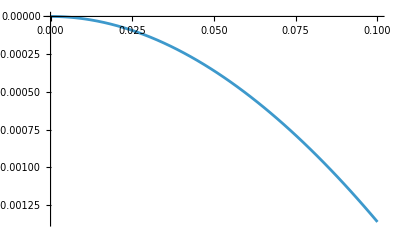

```mathematica
Plot[polfunc[x],{x,0,0.1}]
```